# Video Traking UI

## User Interface for gereic video tracking problems

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
"Colors"->1 (*number of color channels*),"ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
"FrameIdFromFrame"->False
];
```

## Step 1 - Select the video file

```mathematica
VideoSelect[ "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/brightfield_diffusion_channel_low_density_30fps.avi"]
```

brightfield_diffusion_channel_low_density_30fps.avi has 1333 frames and is 720x480

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

(282 | 121
460 | 150)

```mathematica
ROISelect[({{282, 121}, {460, 150}})]
```

(282 | 121
460 | 150)

## Step 3 - Compute the background image

```mathematica
VideoBufferAll[]
```

Buffer: expected 1333 frames. ffmpeg found 1333

Buffer: loaded entire video

```mathematica
bg = BackgroungUpdate[]
```

-Graphics-

## Step 4 - configure tracing algorithm

```mathematica
VideoFindThreshold[]
```

```mathematica
Options[VideoTracking];

SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.6},
 "FilterArea" -> {7,50},
 "UpdateBackgroung" -> False,
 Threshold -> 0.08
]
```

{Threshold→0.08,MinThreshold→0.05,FilterArea→{7,50},FilterElongation→{0.,0.6},AnalysisBlockSize→4000,UpdateBackgroung→False,ForegroundMethod→Bright}

## Step 5 - Inspect per frame basis (run many times!)

```mathematica
<< VideoAnalysis`
```

(1222 | 23.48 | 14.33 | 0. | 1. | 1.89 | 0.01 | 0.48
1222 | 109.13 | 12.5 | 0. | 1. | 1.66 | 3.11 | 0.11)

-Graphics-

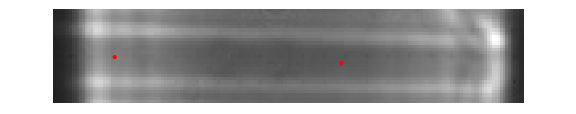

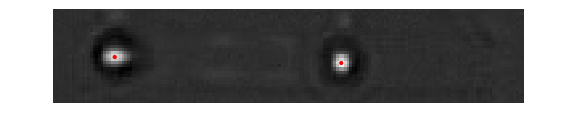

-Graphics-

Area→{1→44.875,2→32.625}

Elongation→{1→0.440263,2→0.0412085}

```mathematica
frame =1222;
If[0>frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]

ShowTrackOverlayed[ VideoGet[frame] , curPos]
ShowTrackOverlayed[ BackgroundCurrent[], curPos]
ShowTrackOverlayed[ VideoGetForeground@VideoGet[frame] // ImageAdjust, curPos] 
ShowTrackOverlayed[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] , curPos]

"Area"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Elongation"]
```

## Analyse many videos

```mathematica
ComputeVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder},
Clear[output];
Print@"==============================================";
oldROI = ROICurrent[] ; (*reuse ROI*)

Print @VideoSelect[ file ];

Print["Video lenght (30fps eqv.): "<> ToString@(VideoLength[] /30 // N) <> " sec"];
Print ["ROI: "<> ToString@ROISelect[ oldROI ]];

loadTime = AbsoluteTiming[
VideoBufferAll[];
Print @ BackgroungUpdate[] ;
(*Print @ ImageAdjust@ImageDifference[UpdateBackgroung[bg ],GetFrame[1]];*)
][[1]];

{analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
Print["Particles instances found: " <> ToString@Length@output ];

(*update time and positions to absolute ones*)

cornerPos = ROICurrent[]⟦1⟧;
output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
output⟦All,2⟧ = Round[ output⟦All,2⟧+ cornerPos⟦1⟧ , 0.01]; (*x*)
output⟦All,3⟧ = Round[ output⟦All,3⟧+ cornerPos⟦2⟧, 0.01]; (*y*)

outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

Print["Done: "<>
ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

#### Find files

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=("E:\\Experiments\\Antony\\2015-02-18\\3\\2015_02_18_square_wave_s"~~ToString@#~~".avi")&/@ {7}
```

{E:\Experiments\Antony\2015-02-18\3\2015_02_18_square_wave_s7.avi}

#### Run the analysis

```mathematica
Do[ ComputeVideo[f], {f, analyseTheseFiles }]
```

```mathematica
ComputeVideo["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/brightfield_diffusion_channel_low_density_30fps.avi"]
```

==============================================

brightfield_diffusion_channel_low_density_30fps.avi has 1333 frames and is 720x480

Video lenght (30fps eqv.): 44.4333 sec

ROI: {{282, 121}, {460, 150}}

Buffer: expected 1333 frames. ffmpeg found 1333

Buffer: loaded entire video

-Graphics-

Analysing: frames [1 : 1333]

Analysis took (load + recognition): 8.611914 + 22.782058 = 31.39397 sec

Particles instances found: 2666

Done: /Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/brightfield_diffusion_channel_low_density_30fps.csv